```mathematica
(*w=1*)
g2[b_, la_, k_]:=-(b+la+2k)/Sqrt[2Pi]Exp[(-(b-la)^2)/2]+(b+k)/Sqrt[2Pi] Exp[(-(b+k)^2)/2]+0.5*((b+k)^2+1)(Erf[(b+k)/Sqrt[2]]-Erf[(b-la)/Sqrt[2]]);
betaApprox[b_, la_, k_]:=(-(b-la)/Sqrt[2Pi]Exp[(-(b-la)^2)/2]+(b+k)/Sqrt[2Pi] Exp[(-(b+k)^2)/2])/(Erf[(b+k)/Sqrt[2]]-Erf[(b-la)/Sqrt[2]])+0.5*((b+k)^2-1);
f1[b_, la_, k_, ns_]:=betaApprox[b, la, k] +1-1/(Sqrt[2Pi]ns)((k+la)Exp[(-(b-la)^2)/2](2-(b-la)(k+la)))/(Erf[(b+k)/Sqrt[2]]-Erf[(b-la)/Sqrt[2]]);
f2[b_, la_, k_, ns_]:=1/(Sqrt[2Pi]ns)(2(k+la)Exp[(-(b-la)^2)/2])/(Erf[(b+k)/Sqrt[2]]-Erf[(b-la)/Sqrt[2]]);
q[v_]:=1/2. Erfc[v/Sqrt[2.]];
pActiveU0[b_, k_, la_, ns_, u0_, t_]:=0.5*Erfc[(b-u0 Exp[-g2[b, la, k]t/2/ns])/Sqrt[2(1-Exp[-g2[b, la, k]t/ns])]];
pActiveNonInt[b_, k_, la_, ns_, t_]:=NIntegrate[1/Sqrt[2Pi] Exp[-u0^2/2]pActiveU0[b, k, la, ns, u0, t], {u0, -Infinity, b-la}]+NIntegrate[1/Sqrt[2Pi] Exp[-u0^2/2]pActiveU0[b, k, la, ns, u0, t], {u0, b+k, Infinity}]+(q[b-la]-q[b+k])pActiveU0[b, k, la, ns, b+k, t];
pLeftMargin[v_, nd_, Rnd_, qv_]:=(nd  Exp[-v^2/2])/Sqrt[2Pi](1-qv)^(nd-1)(∏_(m=1)^Rnd qv/(1-qv)*(nd-m)/(Rnd -m+1));
(* P1 in eqn (28), the two definitions of P1 below are equivalent, the first one is faster, but might give wrong result when nd is large (~10000) *)
pActiveInt1[b_, k_, R_, la_,ns_, nd_,t_]:=(1-R)NIntegrate[pLeftMargin[v, nd, R nd, q[v]](1/Sqrt[2.Pi] Exp[-u0^2/2.]pActiveU0[b, k, la, ns, u0, t])/(1-q[v]), {v, -Infinity, Infinity}, {u0, -Infinity, v}]; 
(*pActiveInt1[b_, k_, R_, la_,ns_, nd_,t_]:=((1-R)nd)/(nd-R nd -1) NIntegrate[pActiveU0[b, k, la, ns, Sqrt[2.]InverseErfc[2qmu0], t], {x,0, 1.}, {qmu0, InverseBetaRegularized[x, R nd +1, nd -R nd-1], 1.}];*)
(* P2 in eqn (28) *)
pActiveInt2[b_, k_, R_, la_, ns_, nd_,t_]:= (R-q[b+k])HeavisideTheta[R-q[b+k]]*pActiveU0[b, k, la, ns, b+k, t];
(* P3 in eqn (28) *)
pActiveInt3[b_, k_, R_, la_, ns_, nd_,t_]:=NIntegrate[1/Sqrt[2Pi] Exp[-u0^2/2]pActiveU0[b, k, la, ns, u0, t], {u0, b+k, Infinity}];
(* eqn (28) *)
pActiveInt[b_, k_, R_, la_, ns_, nd_,t_]:=pActiveInt1[b, k, R, la, ns, nd, t]+pActiveInt2[b, k, R, la, ns, nd, t]+pActiveInt3[b, k, R, la, ns, nd, t];(*always make sure that R=0.5*Erfc[(b-la)/Sqrt[2]]*)

(*probability that n dendrites are actitve, pa is the probability that one dendrite is active*)
PnActiveNonInt[nd_, n_, pa_]:=(1-pa)^nd/(n!)(∏_(m=0)^(n-1) (nd-m)pa/(1-pa));
(*Negative result probability. pa is the probability that one dendrite is active, recognition threshold is n0 (the number of active dendrites must be larger than n0) *)
PNegativeNonInt[nd_, n0_, pa_]:=∑_(n=0)^n0 PnActiveNonInt[nd, n, pa];
(*Approximation of PNegativeNonInt by treating binomial distribution like a gaussian distribution*)
PNegativeNonIntGaussian[nd_, n0_, pa_]:=1/2(1+Erf[(n0-pa nd)/Sqrt[2nd (pa-pa^2)]]); 
(*probability that n dendrites are actitve, pa1 is the prob that an originally active dendrite is active, pa2 is the prob that an originally inactive dendrite is active*)
PnActiveInt[nd_, Rnd_, n_, pa1_, pa2_]:= (1-pa1)^Rnd(1-pa2)^(nd-Rnd)∑_(n1=0)^n (1/(n1! (n-n1)!)*(∏_(m1=0)^(n1-1) ((Rnd-m1)pa1)/(1-pa1)) * (∏_(m2=0)^(n-n1-1) ((nd-Rnd-m2)pa2)/(1-pa2)))
(*Negative result probability. Recognition threshold is n0 (the number of active dendrites must be larger than n0) *)
PNegativeInt[nd_, Rnd_, n0_, pa1_, pa2_]:=∑_(n=0)^n0 PnActiveInt[nd, Rnd, n, pa1, pa2];
(*Approximation of PNegativeInt by treating binomial distribution like a gaussian distribution*)
PNegativeIntGaussian[nd_, Rnd_, n0_, pa1_, pa2_]:=1/2(1+Erf[(n0-(Rnd pa1+(nd-Rnd)pa2))/(Sqrt[2]Sqrt[Rnd(pa1-pa1^2)+(nd-Rnd)(pa2-pa2^2)])]);
```

```mathematica
ns=200;nd=300;ndb=3;ndR=2;n0=8;
R=ndR/nd;
b=Sqrt[2]InverseErfc[2ndb/nd];la=InverseErfc[2*ndb/nd]Sqrt[2.]-InverseErfc[2*ndR/nd]Sqrt[2.];
k = 3.;
Solve[-1/(2ns)beta^2+(1-1/ns+f2[b, la, k, ns])beta+(1.-1/ns)==f1[b, la, k, ns], beta]
betaApprox[b, la, k]

decaySteps=10000 ;stepSpacing=100;
timeList = Table[t, {t, 1, decaySteps, stepSpacing}];
```

{{beta→10.2311},{beta→403.737}}

10.2208

```mathematica
fp =PNegativeNonInt[nd*1.0, n0, ndb/nd]
```

0.996397

```mathematica
paNonIntList = Thread[pActiveNonInt[b, k, la, ns, timeList]];
pa1IntList = Thread[(pActiveInt2[b, k, R, la, ns, nd,timeList]+pActiveInt3[b, k, R, la, ns, nd,timeList])/R];
pa2IntList = Thread[pActiveInt1[b, k, R, la, ns, nd,timeList]/(1-R)];
```

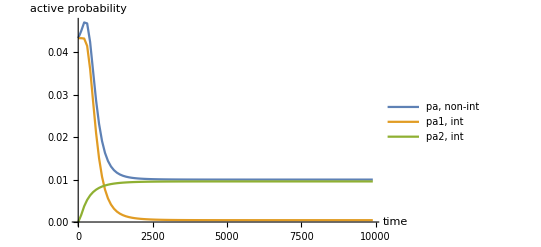

```mathematica
ListLinePlot[{Transpose[{timeList, paNonIntList}], Transpose[{timeList, pa1IntList*R}], Transpose[{timeList, pa2IntList*(1-R)}]}, AxesLabel->{"time", "active probability"}, PlotLegends->{"pa, non-int", "pa1, int", "pa2, int"}, PlotRange->All]
```

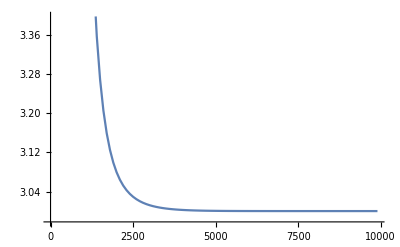

```mathematica
meanListInt = Transpose[{timeList, pa1IntList*ndR+pa2IntList*(nd-ndR)}];
ListLinePlot[meanListInt]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 3.90141×10^-12+ComplexInfinity+ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 3.61366×10^-18+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

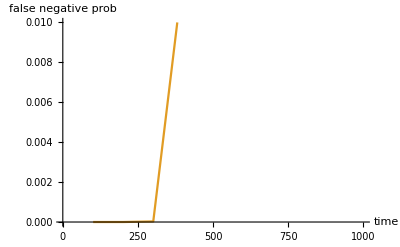

```mathematica
pNegativeNonIntList = Thread[PNegativeNonInt[nd, n0, paNonIntList]];
pNegativeIntList = Thread[PNegativeInt[nd, ndR, n0, pa1IntList, pa2IntList]];
ListLinePlot[{Transpose[{timeList, pNegativeNonIntList}],Transpose[{timeList, pNegativeIntList}]}, AxesLabel->{"time", "false negative prob"}, PlotRange->{{0, 1000}, {0,0.01}}]
```